### Categorization

Tutorial

NounouM2

NounouM2`

NounouM2/tutorial/Load MiCam images (.GSD) and plot

### Keywords

Details

# Load MiCam images (.GSD) and plot

XXXX | XXXX
XXXX | XXXX
XXXX | XXXX

XXXX.

Initialize Package

```mathematica
<<NounouM2`
```

Welcome to NounouM2, the Mathematica interface to nounou!

( last updated:  Mon 3 Mar 2014 22:06:19 )

( current Git HEAD:  c1b623a1c1f703ddee3ec7367c20c50915fc6ff2 )

( http://github.org/ktakagaki/nounoum )

<<Set JLink` java stack size to 6144Mb>>

```mathematica
(*This will allow one to see logging traces and errors*)
(*On windows, the content of these logs will be output to the default user directory as a text file*)
ShowJavaConsole[]
```

«JavaObject[com.wolfram.jlink.ui.ConsoleWindow]»

Load Data Files

```mathematica
nnDataDirectory = "E:\\data\\Micam\\dc-stimulation\\140224"
```

E:\data\Micam\dc-stimulation\140224

```mathematica
(*The $NNReader object is initialized by default upon calling <<NounouM2`*)
(*The object starts out empty*)
(*Further reader objects can be created, using the Java constructor, but beware of having too many readers with too many open data files---and running out of memory*)
$NNReader@load[nnDataDirectory<>"\\mag140224006A.gsd"]
```

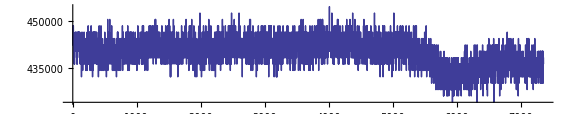

```mathematica
ListLinePlot[$NNReader@data[]@readTraceAbsA[62*92+42-1, NN`frameRangeAll[]],PlotRange->All, AspectRatio->1/5, ImageSize->72*8]
```

```mathematica
ListLinePlot[$NNReader@dataORI[]@readTraceAbsA[62*92+42-1, NN`frameRangeAll[]],PlotRange->All, AspectRatio->1/5, ImageSize->72*8]
```

-Graphics-

More About

Related Tutorials

Related Wolfram Education Group Courses